```mathematica
(*Set Up Parameters*)
r=.;
c=.;
Nt = 200;
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;

Nx = 200; 
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 

c =  1;
c * (deltat / deltax)
```

1

```mathematica
rs = Table[0.1*i,{i,1,30}];

maxevalsCN = Table[0,{i,1,Length[rs]}];
maxevalsEuler = Table[0,{i,1,Length[rs]}];
maxevalsP = Table[0,{i,1,Length[rs]}];

(*Cases not yet Implemented*)
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsRK4 = Table[0,{i,1,Length[rs]}];
```

```mathematica
(*Set up Partial Inversion Matrix*)

(*How many points to the left and right are you picking*)
selectwidth = 8;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

Subscript[δ, i_,j_]:=KroneckerDelta[i,j]

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(*L Matrix for stencil*)
(LP=NDSolve`FiniteDifferenceDerivative[1,grid,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/Δx*)
r=.;
LPX = LP*-1*c*r*Δx;

(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-LPX/2 ].(IP+LPX/2));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,0,Nx},{j,0,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx},{j,0,Nx}];*)

(*WITH Periodic Boundary Conditions*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx},{j,0,Nx}];
```

```mathematica
Do[
(*Change deltat as you loop through different CFL Numbers. Keep deltax fixed!*)
deltat = deltax * rs[[p]];

(*Set Up Grid*)
T = Table[tn = ti + n *deltat, {n, 0, Nt }];

(*For Perodic Interpolation*) 
X = Table[xm = xi + m *deltax, {m, 0, Nx + 1}];
(*For Everything Else*)
X2 =  Table[xm = xi + m *deltax, {m, 0, Nx }];

(************************************************************************************************************)


(*Crank–Nicolson Method*)
LCN = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LCNX = LCN * c * -1 * deltat;
ICN = IdentityMatrix[Length[LCNX]];
A = ICN - ((LCNX / 2));
B = ICN + ((LCNX / 2));
MCN = Inverse[A].B;

(*Euler*)
Leuler = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LEX = Leuler * c * -1 * deltat ;
Ieuler = IdentityMatrix[Length[LEX]];
euler = Ieuler + LEX;

(*Set up done for Partial Inversion before loop*)

(************************************************************************************************************)

(*Eigenvalues*)

(*CN*)
evals = Abs[Eigenvalues[N[MCN]]];
maxevalsCN[[p]] = Max[evals];

(*Euler*)
evalsEuler = Abs[Eigenvalues[N[euler]]];
maxevalsEuler[[p]] = Max[evalsEuler];

(*Partial Inversion*)
evalsP = Abs[Eigenvalues[N[MP//.{r-> (rs[[p]])}]]];
maxevalsP[[p]] = Max[evalsP];



,{p,1,Length[rs]}]
```

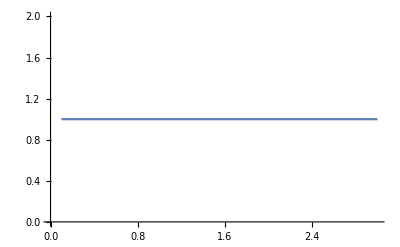

```mathematica
ListPlot[Transpose[{rs,maxevalsCN}], Joined->True]
```

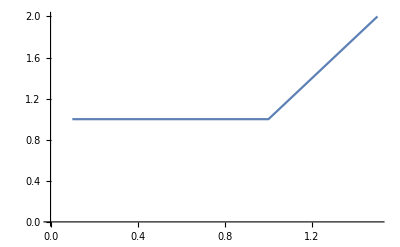

```mathematica
ListPlot[Transpose[{rs,maxevalsEuler}], Joined->True, PlotRange->{{0,1.5},{0,2}}]
```

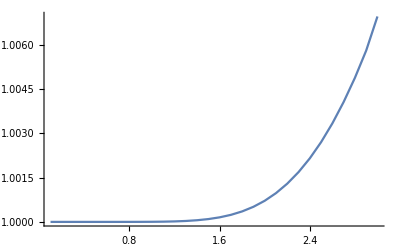

```mathematica
ListPlot[Transpose[{rs,maxevalsP}], Joined->True, PlotRange->All]
```

```mathematica
NumberForm[maxevalsP,16]
```

{1.00000000000001,1.000000000000708,1.000000000039433,1.00000000066372,1.000000005776529,1.000000032975279,1.000000140232216,1.000000479547775,1.000001385821194,1.000003502199438,1.000007933405492,1.000016409219957,1.000031434494665,1.000056401549074,1.000095645454574,1.000154430983707,1.000238869642608,1.000355774081499,1.000512463802206,1.000716539791028,1.000975646562843,1.001297238656605,1.00168836563899,1.002155485922578,1.002704315829872,1.003339716791468,1.004065620623502,1.00488499059861,1.005809247999548,1.006965139421657}